```mathematica
ClearAll["Global`*"];
 Remove["Global`*"];
Quiet[Get["D:\\Users\\daniel\\Documents\\Wolfram Mathematica\\álgebra abstracta computacional\\Analyzer\\SACNA.wl"]]
```

```mathematica
(*Red Omega 6*)
Reacciones = {"2L2 ->L4","2D2->D4", "L2+L4->L6","D2+D4->D6","L4->2L2","D4->2D2","L6->L2+L4","D6->D2+D4","Z2->L2","Z2->D2","L2->Z2","D2->Z2","Z2+L2->L4","Z2+D2->D4","Z2+L4->L6","Z2+D4->D6"};
rates={ε,ε,ε,ε,β,β,β,β,μ,μ,ν,ν,α,α,α,α};
(*rates={};*)
tiempo=1;
Quiet[RunSemiAlgebraicAnalysis[Reacciones,rates,tiempo]];
```

Reacciones ingresadas

{2L2 ->L4,2D2->D4,L2+L4->L6,D2+D4->D6,L4->2L2,D4->2D2,L6->L2+L4,D6->D2+D4,Z2->L2,Z2->D2,L2->Z2,D2->Z2,Z2+L2->L4,Z2+D2->D4,Z2+L4->L6,Z2+D4->D6}

Clausura Quiral de las reacciones ingresadas

{2L2->L4,2D2->D4,L2+L4->L6,D2+D4->D6,L4->2L2,D4->2D2,L6->L2+L4,D6->D2+D4,Z2->L2,Z2->D2,L2->Z2,D2->Z2,L2+Z2->L4,D2+Z2->D4,L4+Z2->L6,D4+Z2->D6}

Revisión de la sintaxis de las reacciones ingresadas

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Constantes de las reacciones

{ε,ε,ε,ε,β,β,β,β,μ,μ,ν,ν,α,α,α,α}

{ε,ε,ε,ε,β,β,β,β,μ,μ,ν,ν,α,α,α,α}

Especies

{D2,D4,D6,L2,L4,L6,Z2}

Ecuaciones del sistema

{-D2 Z2 α+2 D4 β+D6 β-2 D2^2 ε-D2 D4 ε+Z2 μ-D2 ν,D2 Z2 α-D4 Z2 α-D4 β+D6 β+D2^2 ε-D2 D4 ε,D4 Z2 α-D6 β+D2 D4 ε,-L2 Z2 α+2 L4 β+L6 β-2 L2^2 ε-L2 L4 ε+Z2 μ-L2 ν,L2 Z2 α-L4 Z2 α-L4 β+L6 β+L2^2 ε-L2 L4 ε,L4 Z2 α-L6 β+L2 L4 ε,-D2 Z2 α-D4 Z2 α-L2 Z2 α-L4 Z2 α-2 Z2 μ+D2 ν+L2 ν}==0

Sustituciones racémicas

{L2→D2,L4→D4,L6→D6}

{-D2 Z2 α+2 D4 β+D6 β-2 D2^2 ε-D2 D4 ε+Z2 μ-D2 ν,D2 Z2 α-D4 Z2 α-D4 β+D6 β+D2^2 ε-D2 D4 ε,D4 Z2 α-D6 β+D2 D4 ε,-D2 Z2 α+2 D4 β+D6 β-2 D2^2 ε-D2 D4 ε+Z2 μ-D2 ν,D2 Z2 α-D4 Z2 α-D4 β+D6 β+D2^2 ε-D2 D4 ε,D4 Z2 α-D6 β+D2 D4 ε,-2 D2 Z2 α-2 D4 Z2 α-2 Z2 μ+2 D2 ν}==0

Condiciones racémicas

L2==D2&&L4==D4&&L6==D6

Matriz Jacobiana del sistema

(-Z2 α-4 D2 ε-D4 ε-ν | 2 β-D2 ε | β | 0 | 0 | 0 | -D2 α+μ
Z2 α+2 D2 ε-D4 ε | -Z2 α-β-D2 ε | β | 0 | 0 | 0 | D2 α-D4 α
D4 ε | Z2 α+D2 ε | -β | 0 | 0 | 0 | D4 α
0 | 0 | 0 | -Z2 α-4 L2 ε-L4 ε-ν | 2 β-L2 ε | β | -L2 α+μ
0 | 0 | 0 | Z2 α+2 L2 ε-L4 ε | -Z2 α-β-L2 ε | β | L2 α-L4 α
0 | 0 | 0 | L4 ε | Z2 α+L2 ε | -β | L4 α
-Z2 α+ν | -Z2 α | 0 | -Z2 α+ν | -Z2 α | 0 | -D2 α-D4 α-L2 α-L4 α-2 μ)

Matriz Jacobiana del sistema con sustitución de las condiciones racémicas

(-Z2 α-4 D2 ε-D4 ε-ν | 2 β-D2 ε | β | 0 | 0 | 0 | -D2 α+μ
Z2 α+2 D2 ε-D4 ε | -Z2 α-β-D2 ε | β | 0 | 0 | 0 | D2 α-D4 α
D4 ε | Z2 α+D2 ε | -β | 0 | 0 | 0 | D4 α
0 | 0 | 0 | -Z2 α-4 D2 ε-D4 ε-ν | 2 β-D2 ε | β | -D2 α+μ
0 | 0 | 0 | Z2 α+2 D2 ε-D4 ε | -Z2 α-β-D2 ε | β | D2 α-D4 α
0 | 0 | 0 | D4 ε | Z2 α+D2 ε | -β | D4 α
-Z2 α+ν | -Z2 α | 0 | -Z2 α+ν | -Z2 α | 0 | -2 D2 α-2 D4 α-2 μ)

Matriz A

(-Z2 α-4 D2 ε-D4 ε-ν | 2 β-D2 ε | β
Z2 α+2 D2 ε-D4 ε | -Z2 α-β-D2 ε | β
D4 ε | Z2 α+D2 ε | -β)

Matriz B

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

Matriz A+B

(-Z2 α-4 D2 ε-D4 ε-ν | 2 β-D2 ε | β
Z2 α+2 D2 ε-D4 ε | -Z2 α-β-D2 ε | β
D4 ε | Z2 α+D2 ε | -β)

Matriz A-B

(-Z2 α-4 D2 ε-D4 ε-ν | 2 β-D2 ε | β
Z2 α+2 D2 ε-D4 ε | -Z2 α-β-D2 ε | β
D4 ε | Z2 α+D2 ε | -β)

Matriz A-B-Δ

(-Z2 α-δ2-4 D2 ε-D4 ε-ν | 2 β-D2 ε | β
Z2 α+2 D2 ε-D4 ε | -Z2 α-β-δ4-D2 ε | β
D4 ε | Z2 α+D2 ε | -β-δ6)

Condiciones para la estabilidad en el caso de reacción difusión para la matriz A+B

{True,True,-Z2^2 α^2 β-Z2 α β^2-2 D2 Z2 α β ε+β^2 ν≥0}

Condiciones para la estabilidad en el caso de reacción difusión para la matriz A-B

{True,True,-Z2^2 α^2 β-Z2 α β^2-2 D2 Z2 α β ε+β^2 ν≥0}

Condiciones para la inestabilidad en el caso de reacción difusión para la matriz A-B-Δ

{False,False,-Z2^2 α^2 β-Z2 α β^2+β^2 δ2+Z2 α β δ4+β δ2 δ4+Z2^2 α^2 δ6-Z2 α β δ6+Z2 α δ2 δ6+β δ2 δ6+Z2 α δ4 δ6+δ2 δ4 δ6-2 D2 Z2 α β ε+4 D2 β δ4 ε+6 D2 Z2 α δ6 ε+D4 Z2 α δ6 ε+3 D4 β δ6 ε+D2 δ2 δ6 ε+4 D2 δ4 δ6 ε+D4 δ4 δ6 ε+6 D2^2 δ6 ε^2+β^2 ν+β δ4 ν+Z2 α δ6 ν+β δ6 ν+δ4 δ6 ν+D2 δ6 ε ν<0}

Condiciones para la inestabilidad en el caso de reacción difusión para la matriz A-B

{False,False,-Z2^2 α^2 β-Z2 α β^2-2 D2 Z2 α β ε+β^2 ν<0}

Condiciones Semialgebraicas del sistema reacción-difusión

D2≥0&&D4≥0&&D6≥0&&Z2≥0&&α>0&&β>0&&ε>0&&μ>0&&ν>0&&β (Z2^2 α^2+Z2 α (β+2 D2 ε)-β ν)≤0&&δ2≥0&&δ4≥0&&δ6≥0&&2 D4 β+D6 β+Z2 μ==D2 (Z2 α+2 D2 ε+D4 ε+ν)&&D2 Z2 α+D6 β+D2^2 ε==D4 (Z2 α+β+D2 ε)&&D6 β==D4 (Z2 α+D2 ε)&&Z2 (D2 α+D4 α+μ)==D2 ν&&Z2^2 α^2 (-β+δ6)+β^2 (δ2+ν)+β (δ2 (δ4+δ6)+4 D2 δ4 ε+3 D4 δ6 ε+δ4 ν+δ6 ν)+δ6 (6 D2^2 ε^2+δ2 (δ4+D2 ε)+D2 ε (4 δ4+ν)+δ4 (D4 ε+ν))+Z2 α (-β^2+β (δ4-δ6-2 D2 ε)+δ6 (δ2+δ4+6 D2 ε+D4 ε+ν))<0

Solución del sistema reacción-difusión

{False,-D2==0||-D4==0||-D6==0||-Z2==0||-δ2==0||-δ4==0||-δ6==0||D2 Z2 α-2 D4 β-D6 β+2 D2^2 ε+D2 D4 ε-Z2 μ+D2 ν==0||Z2^2 α^2+Z2 α β+2 D2 Z2 α ε-β ν==0}

Por ejemplo

Se alcanzó el tiempo impuesto sin llegar a una solución

Condiciones semialgebraicas del sistema reacción

D2≥0&&D4≥0&&D6≥0&&Z2≥0&&α>0&&β>0&&ε>0&&μ>0&&ν>0&&2 D4 β+D6 β+Z2 μ==D2 (Z2 α+2 D2 ε+D4 ε+ν)&&D2 Z2 α+D6 β+D2^2 ε==D4 (Z2 α+β+D2 ε)&&D6 β==D4 (Z2 α+D2 ε)&&Z2 (D2 α+D4 α+μ)==D2 ν&&β (Z2^2 α^2+Z2 α (β+2 D2 ε)-β ν)>0

Solución del sistema reacción

D2>0&&D4>0&&D6==D4^2/D2&&Z2>0&&α>0&&β>(D4 Z2 α)/D6&&ε==(-D4 Z2 α+D6 β)/(D2 D4)&&0<μ<(D2 Z2^2 α^2+2 D2 Z2 α β-2 D4 β^2-D6 β^2+2 D2^2 Z2 α ε+2 D2^2 β ε+D2 D4 β ε)/(Z2 β)&&ν==-(D2 Z2 α-2 D4 β-D6 β+2 D2^2 ε+D2 D4 ε-Z2 μ)/D2

Por ejemplo

{D2→4,D4→2,D6→1,Z2→1,α→1,β→8,ε→3/4,μ→1,ν→7/4}

{ε,β,μ,ν,α}

{D2,D4,D6,L2,L4,L6,Z2}

{ε→3/4,β→8,μ→1,ν→4.05,α→1}

Ecuaciones diferenciales

{-4.05 D2[t]-(3 D2[t]^2)/2+16 D4[t]-3/4 D2[t] D4[t]+8 D6[t]+Z2[t]-D2[t] Z2[t]==D2'[t],(3 D2[t]^2)/4-8 D4[t]-3/4 D2[t] D4[t]+8 D6[t]+D2[t] Z2[t]-D4[t] Z2[t]==D4'[t],3/4 D2[t] D4[t]-8 D6[t]+D4[t] Z2[t]==D6'[t],-4.05 L2[t]-(3 L2[t]^2)/2+16 L4[t]-3/4 L2[t] L4[t]+8 L6[t]+Z2[t]-L2[t] Z2[t]==L2'[t],(3 L2[t]^2)/4-8 L4[t]-3/4 L2[t] L4[t]+8 L6[t]+L2[t] Z2[t]-L4[t] Z2[t]==L4'[t],3/4 L2[t] L4[t]-8 L6[t]+L4[t] Z2[t]==L6'[t],4.05 D2[t]+4.05 L2[t]-2 Z2[t]-D2[t] Z2[t]-D4[t] Z2[t]-L2[t] Z2[t]-L4[t] Z2[t]==Z2'[t]}

Condiciones Iniciales

{D2[0]==4,D4[0]==2.00001,D6[0]==1,L2[0]==4,L4[0]==2,L6[0]==1,Z2[0]==1}

Species Concentrations Graphic

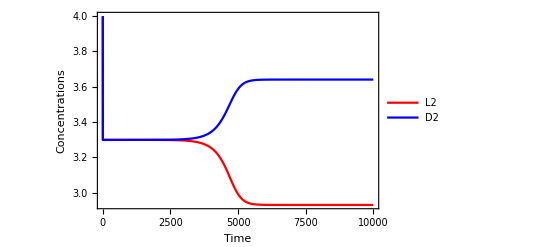

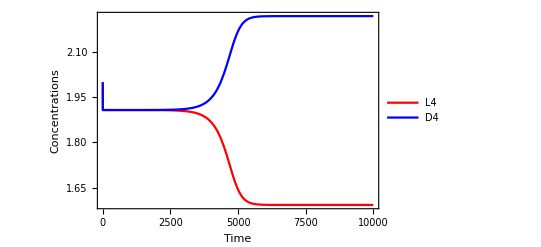

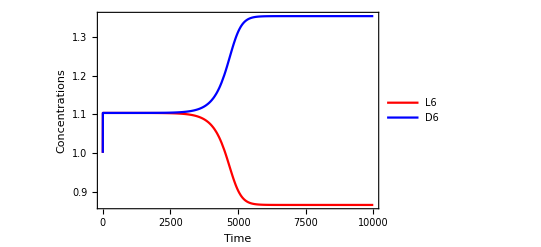

```mathematica
ReactionSystemSimulator[Reacciones,rates,{3/4,8,1,4.05,1},{4,2.00001,1,4,2,1,1},t,0,10000];
```

```mathematica
ratesInitialValues={1,1,1,1,1};
concentrationsInitialValues={2+0.000001,2*(2+0.25*Sqrt[65]-1.75)+0.000001,1+0.25*Sqrt[65]-1.75,2,2*(2+0.25*Sqrt[65]-1.75),1+0.25*Sqrt[65]-1.75,0.25*Sqrt[65]-1.75};
diffusionValues={0.5*(0.25*Sqrt[65]-1.75)^2+0.625*Sqrt[65]-39/8,0,0,0.5*(0.25*Sqrt[65]-1.75)^2+0.625*Sqrt[65]-39/8,0,0,0};
ReactionDiffusionSystemSimulator[Reacciones,rates,ratesInitialValues,concentrationsInitialValues,diffusionValues,x,t,0,100];
```

{ε,β,μ,ν,α}

{ε→1,β→1,μ→1,ν→1,α→1}

{D2,D4,D6,L2,L4,L6,Z2}

{δD2,δD4,δD6,δL2,δL4,δL6,δZ2}

{δD2→0.199173,δD4→0,δD6→0,δL2→0.199173,δL4→0,δL6→0,δZ2→0}

Ecuaciones diferenciales parciales

{-D2[t,x]-2 D2[t,x]^2+2 D4[t,x]-D2[t,x] D4[t,x]+D6[t,x]+Z2[t,x]-D2[t,x] Z2[t,x]+0.03967 D2^(0,2)[t,x]==D2^(1,0)[t,x],D2[t,x]^2-D4[t,x]-D2[t,x] D4[t,x]+D6[t,x]+D2[t,x] Z2[t,x]-D4[t,x] Z2[t,x]==D4^(1,0)[t,x],D2[t,x] D4[t,x]-D6[t,x]+D4[t,x] Z2[t,x]==D6^(1,0)[t,x],-L2[t,x]-2 L2[t,x]^2+2 L4[t,x]-L2[t,x] L4[t,x]+L6[t,x]+Z2[t,x]-L2[t,x] Z2[t,x]+0.03967 L2^(0,2)[t,x]==L2^(1,0)[t,x],L2[t,x]^2-L4[t,x]-L2[t,x] L4[t,x]+L6[t,x]+L2[t,x] Z2[t,x]-L4[t,x] Z2[t,x]==L4^(1,0)[t,x],L2[t,x] L4[t,x]-L6[t,x]+L4[t,x] Z2[t,x]==L6^(1,0)[t,x],D2[t,x]+L2[t,x]-2 Z2[t,x]-D2[t,x] Z2[t,x]-D4[t,x] Z2[t,x]-L2[t,x] Z2[t,x]-L4[t,x] Z2[t,x]==Z2^(1,0)[t,x]}

Condiciones iniciales temporales

{D2[0,x]==2.,D4[0,x]==4.53113,D6[0,x]==1.26556,L2[0,x]==2,L4[0,x]==4.53113,L6[0,x]==1.26556,Z2[0,x]==0.265564}

-Graphics3D-

-Graphics3D-

-Graphics3D-